# Modelo versión 3

## Importación de la red:

Pasar a SetDirectory el directorio en donde se encuentra el archivo .graphml para facilidad

Tener en cuenta que i debe cumplir con los valores de num-people

```mathematica
SetDirectory[NotebookDirectory[]];
```

Todas las redes:

```mathematica
networksM3=Table[Import[StringJoin["graphs/model-v3/","network-",IntegerString[i],".graphml"]],{i,0,100,10}];
```

```mathematica
clusteringM3=Map[GlobalClusteringCoefficient,Flatten[networksM3,1]];
aplM3=Map[MeanGraphDistance,Flatten[networksM3,1]];
```

## Graficos:

```mathematica
axes=Table[{i,j},{i,0,100,10},{j,0.1,1,0.1}];
clusteringPlotM3=Table[Join[Flatten[axes,1][[c]],{clusteringM3[[c]]}],{c,1,Length[clusteringM3],1}];
ListPlot3D[clusteringPlotM3,ColorFunction->"SouthwestColors"]
```

```mathematica
pathPlotM3=Table[Join[Flatten
[axes,1][[c]],{pathPlotM3[[c]]}],{c,1,Length[aplM3],1}];
ListPlot3D[pathPlotM3,ColorFunction->"SouthwestColors"]
```

# “PRUEBAS DE JUGUETE”

## num-people=50 capacity=[1-50] Varia unidades de tiempo

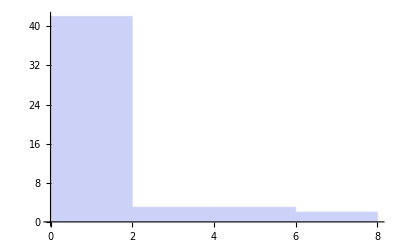

```mathematica
network10=Import["graphs/model-v3/network-50-50-10.graphml"];
Histogram[VertexDegree[network10]]
```

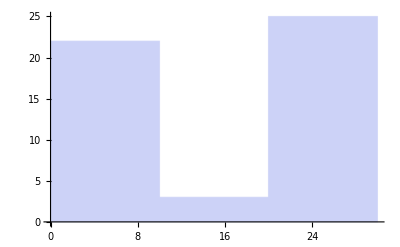

```mathematica
network50=Import["graphs/model-v3/network-50-50-50.graphml"];
Histogram[VertexDegree[network50]]
```

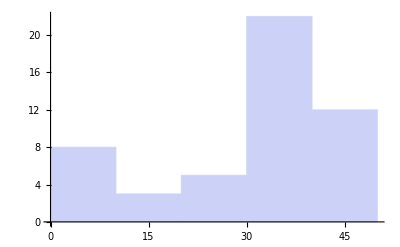

```mathematica
network100=Import["graphs/model-v3/network-50-50-100.graphml"];
Histogram[VertexDegree[network100]]
```

## num-people=500 capacity=[1-50] Varia unidades de tiempo

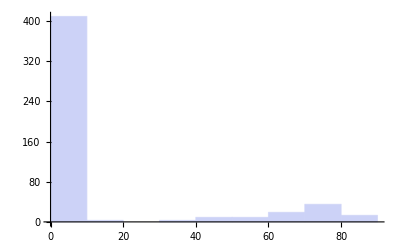

```mathematica
network100=Import["graphs/model-v3/network-500-50-100.graphml"];
Histogram[VertexDegree[network100]]
```

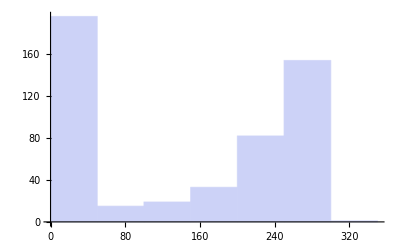

```mathematica
network500=Import["graphs/model-v3/network-500-50-500.graphml"];
Histogram[VertexDegree[network500]]
```

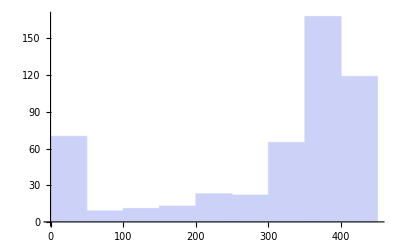

```mathematica
network1000=Import["graphs/model-v3/network-500-50-1000.graphml"];
Histogram[VertexDegree[network1000]]
```

## num-people=50 capacity=[1-25] Varia unidades de tiempo

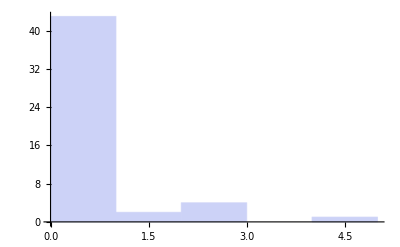

```mathematica
network10=Import["graphs/model-v3/network-50-25-10.graphml"];
Histogram[VertexDegree[network10]]
```

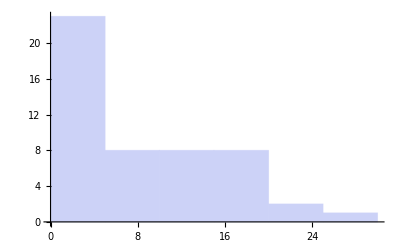

```mathematica
network50=Import["graphs/model-v3/network-50-25-50.graphml"];
Histogram[VertexDegree[network50]]
```

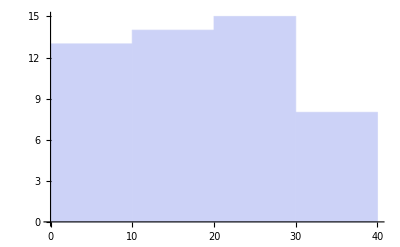

```mathematica
network100=Import["graphs/model-v3/network-50-25-100.graphml"];
Histogram[VertexDegree[network100]]
```

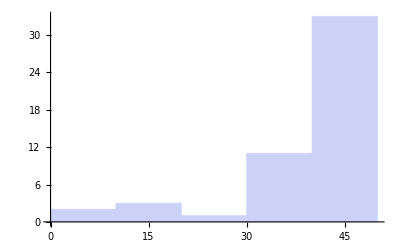

```mathematica
network200=Import["graphs/model-v3/network-50-25-200.graphml"];
Histogram[VertexDegree[network200]]
```

## num-people=500 capacity=[1-25] Varia unidades de tiempo

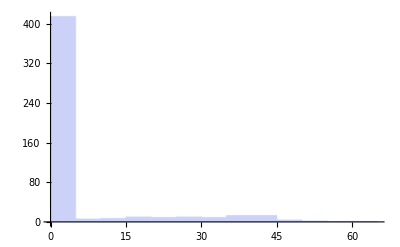

```mathematica
network100=Import["graphs/model-v3/network-500-25-100.graphml"];
Histogram[VertexDegree[network100]]
```

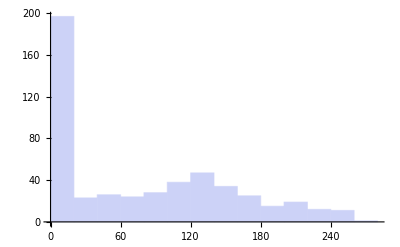

```mathematica
network500=Import["graphs/model-v3/network-500-25-500.graphml"];
Histogram[VertexDegree[network500]]
```

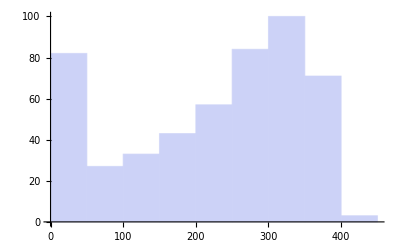

```mathematica
network1000=Import["graphs/model-v3/network-500-25-1000.graphml"];
Histogram[VertexDegree[network1000]]
```

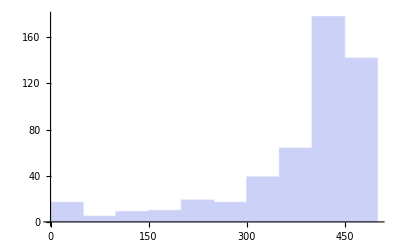

```mathematica
network2000=Import["graphs/model-v3/network-500-25-2000.graphml"];
Histogram[VertexDegree[network2000]]
```

## num-people=50 capacity=[1-15] Varia unidades de tiempo

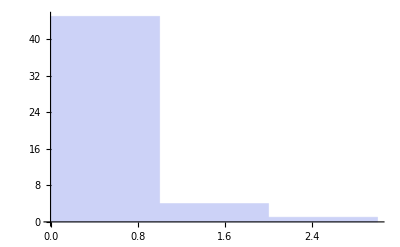

```mathematica
network10=Import["graphs/model-v3/network-50-15-10.graphml"];
Histogram[VertexDegree[network10]]
```

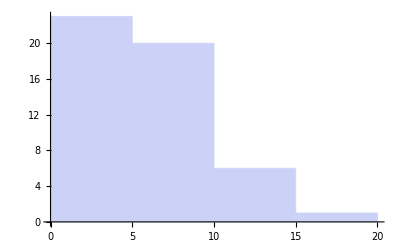

```mathematica
network50=Import["graphs/model-v3/network-50-15-50.graphml"];
Histogram[VertexDegree[network50]]
```

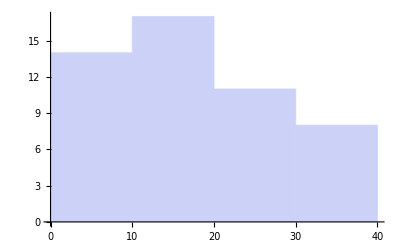

```mathematica
network100=Import["graphs/model-v3/network-50-15-100.graphml"];
Histogram[VertexDegree[network100]]
```

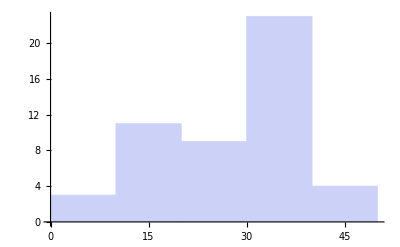

```mathematica
network200=Import["graphs/model-v3/network-50-15-200.graphml"];
Histogram[VertexDegree[network200]]
```

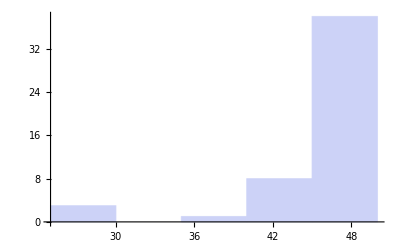

```mathematica
network400=Import["graphs/model-v3/network-50-15-400.graphml"];
Histogram[VertexDegree[network400]]
```

## num-people=500 capacity=[1-15] Varia unidades de tiempo

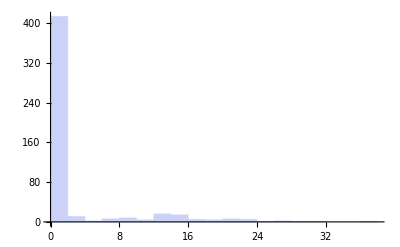

```mathematica
network100=Import["graphs/model-v3/network-500-15-100.graphml"];
Histogram[VertexDegree[network100]]
```

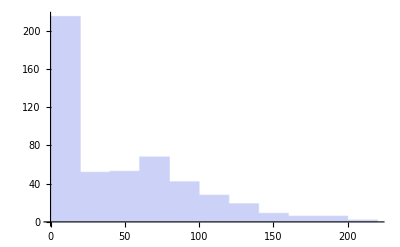

```mathematica
network500=Import["graphs/model-v3/network-500-15-500.graphml"];
Histogram[VertexDegree[network500]]
```

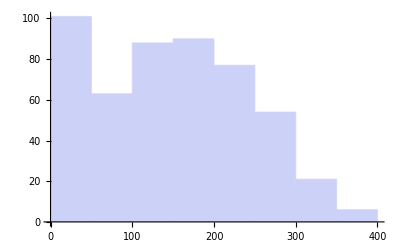

```mathematica
network1000=Import["graphs/model-v3/network-500-15-1000.graphml"];
Histogram[VertexDegree[network1000]]
```

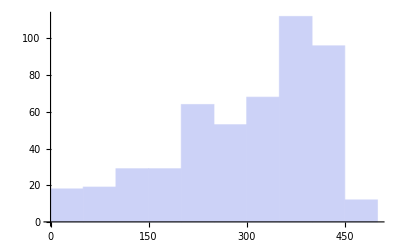

```mathematica
network2000=Import["graphs/model-v3/network-500-15-2000.graphml"];
Histogram[VertexDegree[network2000]]
```

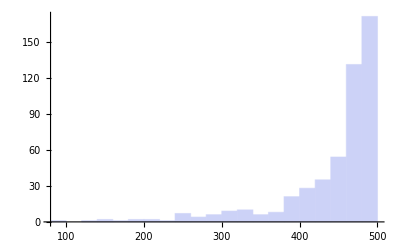

```mathematica
network4000=Import["graphs/model-v3/network-500-15-4000.graphml"];
Histogram[VertexDegree[network4000]]
```

## num-people=1000 capacity=[1-50] t=1000

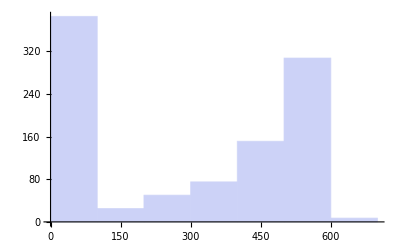

```mathematica
network1000=Import["graphs/model-v3/network-1000-50-1000.graphml"];
Histogram[VertexDegree[network1000]]
```

## num-people=1000 capacity=[1-25] t=2000

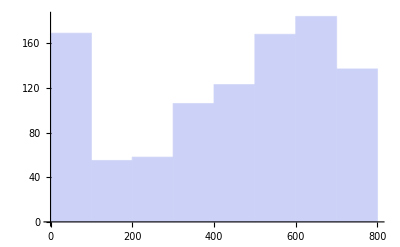

```mathematica
network2000=Import["graphs/model-v3/network-1000-25-2000.graphml"];
Histogram[VertexDegree[network2000]]
```